-Graphics-

# New in 12.1

## Database integration

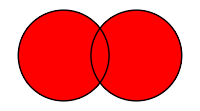
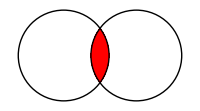
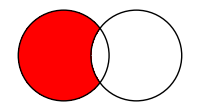
-Graphics-Union-Graphics-Intersection-Graphics-Complement

## Outline

### The Entity Relational Model

### Classes of Entities as a Symbolic Representation of Queries

EntityClass

ExtendedEntityClass

FilteredEntityClass

SortedEntityClass

SampledEntityClass

AggregatedEntityClass

CombinedEntityClass

### EntityFunction

### Set Operations on Entities

### Parametrizing Equality

### EntityProperties of Set Operations

## The Entity Relational Model

```mathematica
EntityRegister[EntityStore[RelationalDatabase[FindFile["ExampleData/ecommerce-database.sqlite"]]]]
```

One main resolver: EntityValue:

```mathematica
EntityValue[
FilteredEntityClass[
"employees" ,
EntityFunction[x, StringStartsQ[x["firstName"],"L"]]
],
{"firstName", "lastName"}
]
```

For the relational experts: projection is always delayed until the very last moment; that is the only thing EntityValue does.

## Classes of Entities as a Symbolic Representation of Queries

Disclaimer: The following examples are meant to show the symbolic representation (I do not guarantee they will yield something sensible).

### EntityClass

Forefather of all the other representations, named and implicit:

```mathematica
EntityClass["Country", "GroupOf8"]
```

```mathematica
EntityClass["Country", "Population" -> GreaterThan[10^9]]
```

### ExtendedEntityClass

Add one or more properties:

```mathematica
ExtendedEntityClass[
"Country",
"ArrivalsDivorceRatio" -> EntityFunction[c, c["AirArrivals"]/c["AnnualDivorces"]]
]
```

### FilteredEntityClass

Filter by an arbitrary predicate:

```mathematica
FilteredEntityClass[
"Country",
EntityFunction[c, c["FemalePopulation"] < c["MalePopulation"] || c["CapitalCity"] ==Entity["City",{"Rome","Lazio","Italy"}]]
]
```

### SortedEntityClass

Sort by a property and limit the output:

```mathematica
SortedEntityClass[
"Country",
"Population" -> "Descending",
{2,5}
]
```

### SampledEntityClass

Limit the output:

```mathematica
SampledEntityClass[
"Country",
3
]
```

### AggregatedEntityClass

Group entities and aggregate properties:

```mathematica
AggregatedEntityClass[
"Country",
"Population" -> Mean,
"Continent"
]
```

### CombinedEntityClass

Combine two entity types into a single one:

```mathematica
CombinedEntityClass[
"Country",
"City",
"CapitalCity" -> "Entity"
]
```

## EntityFunction

A property that is computed on the fly:

```mathematica
Entity["Country","Italy"][
EntityFunction[
c,
c["VehiclesInUsePassengerCars"]/c["VehiclesInUseBuses"]
]
]
```

Can be used anywhere a property can be used:

```mathematica
SortedEntityClass[
"Country",
EntityFunction[
c,
c["VehiclesInUsePassengerCars"]/c["VehiclesInUseBuses"]
] ,
1
]//EntityList
```

## Set Operations on Entities

Three main set operations:

UnionedEntityClass
IntersectedEntityClass
ComplementedEntityClass

Corresponding to:

Union
Intersection
Complement

Equality is defined in the sense of (simplified) EntityList:

```mathematica
EntityList[IntersectedEntityClass[EntityClass["Country","GroupOf8"], EntityClass["Country","EuropeanUnion"]]]===Intersection[EntityList[EntityClass["Country","GroupOf8"]],EntityList[EntityClass["Country","EuropeanUnion"]]]
```

## Parametrizing Equality

Just like set operations take a SameTest option, there is SameTestProperties, which allows you to do very powerful things:

```mathematica
UnionedEntityClass[
"Movie",
"Book",
SameTestProperties -> "Name"
]
```

```mathematica
UnionedEntityClass[EntityClass["Movie","Name"->"The Godfather"],EntityClass["Book","Name"->"The Godfather"], SameTestProperties-> "Name"][{"FirstPublished", "ReleaseDate"}]
```

## Parametrizing Equality (continued in SQL)

SameTestProperties can be set to False, which is equivalent to setting SameTest to Function[False] to get multiple copies (UNION ALL):

```mathematica
UnionedEntityClass[
"offices",
"offices",
SameTestProperties-> False
]["officeCode"]
```

SameTestProperties and a single-argument UnionedEntityClass can be used to effectively perform DeleteDuplicatesBy (DISTINCT ON):

```mathematica
UnionedEntityClass[
"customers",
SameTestProperties->{"country"}
][{"customerName", "country"}]
```

## EntityProperties of Set Operations

Properties that have the same string name get combined, but the old properties are still available:

```mathematica
EntityValue[
UnionedEntityClass["offices","employees"],{
EntityProperty["offices","officeCode"],EntityProperty["employees","officeCode"],
EntityProperty[
UnionedEntityClass["offices","employees"],
"officeCode"
]}
]//TableForm
```